MIT License
Copyright (c) 2021 Gaetana Spedalieri  gae.spedalieri@york.ac.uk

Permission is hereby granted, free of charge, to any person obtaining a copy of this software and associated documentation files (the “Software”), to deal in the Software without restriction, including without limitation the rights to use, copy, modify, merge, publish, distribute, sublicense, and/or sell copies of the Software, and to permit persons to whom the Software is furnished to do so,subject to the following conditions: The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED “AS IS”, WITHOUT WARRANTY OF ANY KIND, EXPRESS OR IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,  FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT. IN NO EVENT SHALL THE AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE SOFTWARE.

Optimal displaced-squeezed probes

```mathematica
Quit[]
```

```mathematica
(**** check of the Pfa and Pmd ****)
```

```mathematica
gauss[z_,zm_,σ_]:=1/(σ  √(2 π))Exp[(-(z-zm)^2)/(2 σ^2)]
```

```mathematica
Simplify[∫_t^(+∞) gauss[z,zm,σ]ⅆz,σ>0]
```

1/2 (1-Erf[(t-zm)/(√2 σ)])

```mathematica
Simplify[∫_(-∞)^t gauss[z,zm,σ]ⅆz,σ>0]
```

1/2 (1+Erf[(t-zm)/(√2 σ)])

```mathematica
Erf[-x]+Erf[x]
```

0

```mathematica
(** evaluation thermal noise **)
```

```mathematica
λNUM=8 10^-7; (* 800 nm *)
Wband = 10^8;  (* 100 MHz *)
aRNUM =  1/10; (*  0.1 ; *)
(* 10 cm *)
```

```mathematica
hplanck=6.62607004 10^-34;
```

```mathematica
cLIGHT=299792458;
νfreq=cLIGHT/λNUM
```

374740572500000

```mathematica
angleVIEW = (1/10) (2 π)/360; (* 1/10 degree *)
```

```mathematica
Ωfov=N[angleVIEW^2]  (* in steradians *)
```

3.04617×10^-6

```mathematica
N[(π  λNUM)/(hplanck cLIGHT) ( 1.5 10^-1)] (* converting units for HskyDay *)
HskyDay=1.9 10^18;  (* Cloudy sky 800 nm *)
Δλ=10^-4; (* in nm - homodyne detector *)
(* Wband=10^8; (* 100 MHz homodyne detector - already defined above *)  *)
ΓR=N[Δλ Wband^-1 Ωfov aRNUM^2]
```

1.89782×10^18

3.04617×10^-20

```mathematica
nback=HskyDay ΓR
```

0.0578773

```mathematica
N[578773/10000000]
```

0.0578773

```mathematica
(**  probabilities **)
```

```mathematica
f[r_]:=(r+r^-1-2)/4
```

```mathematica
Solve[nS-f[r]==0,r]
```

{{r→1+2 nS-2 √(nS+nS^2)},{r→1+2 nS+2 √(nS+nS^2)}}

```mathematica
rmin[nS_]:=1+2 nS-2 √(nS+nS^2)
rmax[nS_]:=1+2 nS+2 √(nS+nS^2)
```

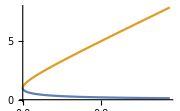

```mathematica
Plot[{rmin[nS],rmax[nS]},{nS,0,1.5},ImageSize->Small]
```

```mathematica
Ω[η_,nS_,nB_,m_,r_,t_]:=Erf[(t-m √(2 η(nS-f[r])))/(√(m (2 nB+1-η(1-r))))]
```

```mathematica
pFA[η0_,nS_,nB_,m_,r_,t_]:=1/2 (1- Ω[η0,nS,nB,m,r,t])
pMD[η1_,nS_,nB_,m_,r_,t_]:=1/2 (1+ Ω[η1,nS,nB,m,r,t])
```

```mathematica
pERR[η0_,η1_,nS_,nB_,m_,r_,t_]:=(pFA[η0,nS,nB,m,r,t]+pMD[η1,nS,nB,m,r,t])/2
```

```mathematica
zmean[η_,nS_,m_,r_]:=m √(2 η (nS-f[r]))
```

```mathematica
(* Testing parameters *)
```

```mathematica
η0num=0;
η1num=2/10;
nBnum=578773/10000000;
nSnum=1/10;
mnum=10; (* testing value only *)
tnum=1; (* threshold value for test *)
ϵ=1/1000; (* needed to avoid numerical problems at the border *)
N[rmin[nSnum]]
N[rmax[nSnum]]
rnum =6/10; (* squeezing for testing = 0.6 *)
N[zmean[η1num,nSnum,mnum,rnum]]
```

0.536675

1.86332

1.1547

```mathematica
(* Explicit optimization of pERR over t - following referee's suggestion *)
```

```mathematica
dpERR[η0_,η1_,nS_,nB_,m_,r_,t_]:=D[pERR[η0,η1,nS,nB,m,r,t],t]
```

```mathematica
Simplify[Solve[dpERR[η0,η1,nS,nB,m,r,t]==0,t]]
```

{{t→-1/(√2 (-1+r) (η0-η1))(m √((2+4 nS-1/r-r) η0)+2 m nB √((2+4 nS-1/r-r) η0)-m √((2+4 nS-1/r-r) η0) η1+m r √((2+4 nS-1/r-r) η0) η1-m √((2+4 nS-1/r-r) η1)-2 m nB √((2+4 nS-1/r-r) η1)+m η0 √((2+4 nS-1/r-r) η1)-m r η0 √((2+4 nS-1/r-r) η1)+√(-1/r m (1+2 nB+(-1+r) η0) (1+2 nB+(-1+r) η1) (m η0-2 m r η0-4 m nS r η0+m r^2 η0+m η1-2 m r η1-4 m nS r η1+m r^2 η1+2 m r √((2+4 nS-1/r-r) η0) √((2+4 nS-1/r-r) η1)-2 (-1+r) r (η0-η1) Log[1+2 nB+(-1+r) η0]+(-1+r) r (η0-η1) Log[m (1+2 nB+(-1+r) η0)]-2 r η0 Log[1+2 nB+(-1+r) η1]+2 r^2 η0 Log[1+2 nB+(-1+r) η1]+2 r η1 Log[1+2 nB+(-1+r) η1]-2 r^2 η1 Log[1+2 nB+(-1+r) η1]+r η0 Log[m (1+2 nB+(-1+r) η1)]-r^2 η0 Log[m (1+2 nB+(-1+r) η1)]-r η1 Log[m (1+2 nB+(-1+r) η1)]+r^2 η1 Log[m (1+2 nB+(-1+r) η1)])))},{t→1/(√2 (-1+r) (η0-η1))(-m √((2+4 nS-1/r-r) η0)-2 m nB √((2+4 nS-1/r-r) η0)+m √((2+4 nS-1/r-r) η0) η1-m r √((2+4 nS-1/r-r) η0) η1+m √((2+4 nS-1/r-r) η1)+2 m nB √((2+4 nS-1/r-r) η1)-m η0 √((2+4 nS-1/r-r) η1)+m r η0 √((2+4 nS-1/r-r) η1)+√(-1/r m (1+2 nB+(-1+r) η0) (1+2 nB+(-1+r) η1) (m η0-2 m r η0-4 m nS r η0+m r^2 η0+m η1-2 m r η1-4 m nS r η1+m r^2 η1+2 m r √((2+4 nS-1/r-r) η0) √((2+4 nS-1/r-r) η1)-2 (-1+r) r (η0-η1) Log[1+2 nB+(-1+r) η0]+(-1+r) r (η0-η1) Log[m (1+2 nB+(-1+r) η0)]-2 r η0 Log[1+2 nB+(-1+r) η1]+2 r^2 η0 Log[1+2 nB+(-1+r) η1]+2 r η1 Log[1+2 nB+(-1+r) η1]-2 r^2 η1 Log[1+2 nB+(-1+r) η1]+r η0 Log[m (1+2 nB+(-1+r) η1)]-r^2 η0 Log[m (1+2 nB+(-1+r) η1)]-r η1 Log[m (1+2 nB+(-1+r) η1)]+r^2 η1 Log[m (1+2 nB+(-1+r) η1)])))}}

```mathematica
tSOL1[η0_,η1_,nS_,nB_,m_,r_]:=-1/(√2 (-1+r) (η0-η1))(m √((2+4 nS-1/r-r) η0)+2 m nB √((2+4 nS-1/r-r) η0)-m √((2+4 nS-1/r-r) η0) η1+m r √((2+4 nS-1/r-r) η0) η1-m √((2+4 nS-1/r-r) η1)-2 m nB √((2+4 nS-1/r-r) η1)+m η0 √((2+4 nS-1/r-r) η1)-m r η0 √((2+4 nS-1/r-r) η1)+√(-1/r m (1+2 nB+(-1+r) η0) (1+2 nB+(-1+r) η1) (m η0-2 m r η0-4 m nS r η0+m r^2 η0+m η1-2 m r η1-4 m nS r η1+m r^2 η1+2 m r √((2+4 nS-1/r-r) η0) √((2+4 nS-1/r-r) η1)-2 (-1+r) r (η0-η1) Log[1+2 nB+(-1+r) η0]+(-1+r) r (η0-η1) Log[m (1+2 nB+(-1+r) η0)]-2 r η0 Log[1+2 nB+(-1+r) η1]+2 r^2 η0 Log[1+2 nB+(-1+r) η1]+2 r η1 Log[1+2 nB+(-1+r) η1]-2 r^2 η1 Log[1+2 nB+(-1+r) η1]+r η0 Log[m (1+2 nB+(-1+r) η1)]-r^2 η0 Log[m (1+2 nB+(-1+r) η1)]-r η1 Log[m (1+2 nB+(-1+r) η1)]+r^2 η1 Log[m (1+2 nB+(-1+r) η1)])))
```

```mathematica
tSOL2[η0_,η1_,nS_,nB_,m_,r_]:=1/(√2 (-1+r) (η0-η1))(-m √((2+4 nS-1/r-r) η0)-2 m nB √((2+4 nS-1/r-r) η0)+m √((2+4 nS-1/r-r) η0) η1-m r √((2+4 nS-1/r-r) η0) η1+m √((2+4 nS-1/r-r) η1)+2 m nB √((2+4 nS-1/r-r) η1)-m η0 √((2+4 nS-1/r-r) η1)+m r η0 √((2+4 nS-1/r-r) η1)+√(-1/r m (1+2 nB+(-1+r) η0) (1+2 nB+(-1+r) η1) (m η0-2 m r η0-4 m nS r η0+m r^2 η0+m η1-2 m r η1-4 m nS r η1+m r^2 η1+2 m r √((2+4 nS-1/r-r) η0) √((2+4 nS-1/r-r) η1)-2 (-1+r) r (η0-η1) Log[1+2 nB+(-1+r) η0]+(-1+r) r (η0-η1) Log[m (1+2 nB+(-1+r) η0)]-2 r η0 Log[1+2 nB+(-1+r) η1]+2 r^2 η0 Log[1+2 nB+(-1+r) η1]+2 r η1 Log[1+2 nB+(-1+r) η1]-2 r^2 η1 Log[1+2 nB+(-1+r) η1]+r η0 Log[m (1+2 nB+(-1+r) η1)]-r^2 η0 Log[m (1+2 nB+(-1+r) η1)]-r η1 Log[m (1+2 nB+(-1+r) η1)]+r^2 η1 Log[m (1+2 nB+(-1+r) η1)])))
```

```mathematica
N[tSOL1[η0num,η1num,nSnum,nBnum,mnum,rnum]]
N[tSOL2[η0num,η1num,nSnum,nBnum,mnum,rnum]]
```

0.415878

31.7932

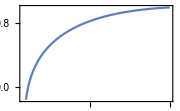

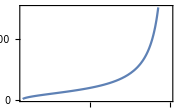

```mathematica
Plot[{N[tSOL1[η0num,η1num,nSnum,nBnum,mnum,r]]},{r,rmin[nSnum]+ϵ,1},ImageSize->Small,Frame->True]
Plot[{N[tSOL2[η0num,η1num,nSnum,nBnum,mnum,r]]},{r,rmin[nSnum]+ϵ,1},ImageSize->Small,Frame->True]
```

```mathematica
N[pERR[η0num,η1num,nSnum,nBnum,mnum,rnum,tSOL1[η0num,η1num,nSnum,nBnum,mnum,rnum]]]
N[pERR[η0num,η1num,nSnum,nBnum,mnum,rnum,tSOL2[η0num,η1num,nSnum,nBnum,mnum,rnum]]]
```

0.401419

0.5

```mathematica
pERRoptimized[η0_,η1_,nS_,nB_,m_,r_]:=pERR[η0,η1,nS,nB,m,r,tSOL1[η0,η1,nS,nB,m,r]]
```

```mathematica
N[pERRoptimized[η0num,η1num,nSnum,nBnum,mnum,rnum]]
```

0.401419

```mathematica
(* symmetric threshold equal to half the mean value *)
```

```mathematica
symthreshold[η0_,η1_,nS_,m_,r_]:=(zmean[η0,nS,m,r]+zmean[η1,nS,m,r])/2
```

```mathematica
tcheck=symthreshold[η0num,η1num,nSnum,mnum,1]
```

1

```mathematica
pcshom[m_,nS_,nB_,η_]:=1/2 Erfc[√((m η nS)/(4 nB+2))] (**check with previous formula for CS + hom**)
```

```mathematica
N[pERR[η0num,η1num,nSnum,nBnum,mnum,1,tcheck]]
N[pcshom[mnum,nSnum,nBnum,η1num]]
```

0.336009

0.336009

```mathematica
(** as a LIDAR - we see that squeezed state + hom beats  coherent state + hom **)
```

```mathematica
(* Minimization over r *)
SqueezedRadar[m_]:=NMinimize[{pERRoptimized[η0num,η1num,nSnum,nBnum,m,r],r>rmin[nSnum]&&r<1},{r}];
```

```mathematica
(* Points for m=1,...,600 *)
(RadarPoints=SqueezedRadar[#]&/@Range[1,600,1];)//AbsoluteTiming//Quiet
```

{86.682,Null}

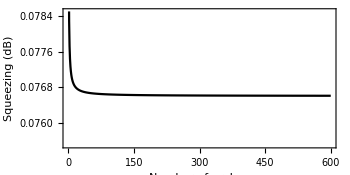

```mathematica
ListPlot[{-10Log10@RadarPoints[[All,2,1,2]]},PlotRange->{0.0755,0.0785},Frame->True,Joined->True,PlotStyle->Black,ImageSize->350,AspectRatio->1/2,PlotRange->All,FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]}]
```

```mathematica
(****** Quantum reading  *****)
```

```mathematica
mnum=1000; (* redefine this parameter here to higher number *)
```

```mathematica
η0num2=90/100;
η1num2=98/100;
nBnum2=nback;
nSnum2=1;
N[rmin[nSnum2]]
N[rmax[nSnum2]]
tmin2[m_]:=zmean[η0num2,nSnum2,m,1]+ϵ
tmax2[m_]:=zmean[η1num2,nSnum2,m,1]-ϵ
```

0.171573

5.82843

```mathematica
(* below we use the more stable version where we extend the upper bound from 1 to rmax; later we double-check that this is OK *)
```

```mathematica
pERRvalueMIN[m_]:=FindMinimum[
pERR[η0num2,η1num2,nSnum2,nBnum2,m,r,t],{r,rmin[nSnum2]+ϵ,rmax[nSnum2]},{t,tmin2[m],tmax2[m]}]
```

```mathematica
pERRscanner[m_]:=pERRvalueMIN[m][[1]]
SqueezeVALscanner[m_]:=pERRvalueMIN[m][[2,1,2]]
```

```mathematica
pERRvalueMIN[mnum]
pERRscanner[mnum]
SqueezeVALscanner[mnum]
-10 Log10[SqueezeVALscanner[mnum]]
```

{0.0609187,{r→0.398555,t→1205.63}}

0.0609187

0.398555

3.99512

```mathematica
pERRscannerCS[m_]:=FindMinimum[
pERR[η0num2,η1num2,nSnum2,nBnum2,m,1,t],{t,tmin2[m],tmax2[m]}][[1]]
```

```mathematica
pERRscannerCS[mnum]
```

0.10834

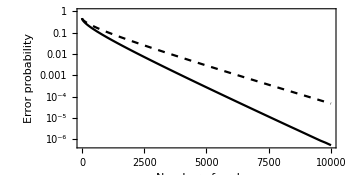

```mathematica
PicRead1=LogPlot[{pERRscanner[m],pERRscannerCS[m]},{m,1,10000},PlotStyle->{Black,{Black,Dashed}},ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Error probability",FontSize->12,FontFamily->"Helvetica"]},AspectRatio->1/2]
```

```mathematica
(* Confirmation of the results with other approach *)
```

```mathematica
pERRreading[m_,r_]:=pERRoptimized[η0num2,η1num2,nSnum2,nBnum2,m,r]
```

```mathematica
pERRreading[mnum,rnum]
```

0.0713369

```mathematica
SqueezedReading[m_]:=NMinimize[{pERRreading[m,r],r>rmin[nSnum2]&&r<1},{r}];
```

```mathematica
SqueezedReading[mnum]
SqueezedReading[mnum][[1]] (* value of probability *)
SqueezedReading[mnum][[2,1,2]] (* value of squeezing *)
```

{0.0609187,{r→0.398552}}

0.0609187

0.398552

```mathematica
step=10000/100;
```

```mathematica
(ReadingPoints={#,SqueezedReading[#][[1]]}&/@Range[1,10001,step];)//AbsoluteTiming//Quiet
```

{20.4502,Null}

```mathematica
(* ReadingPoints[[All]] *)
```

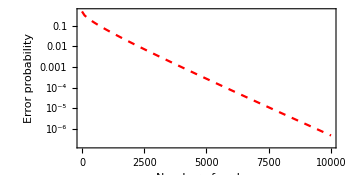

```mathematica
PicRead2=ListLogPlot[{ReadingPoints[[All]]},PlotRange->All,ImageSize->350,Frame->True,
FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Error probability",FontSize->12,FontFamily->"Helvetica"]},AspectRatio->1/2,Joined->True,PlotStyle->{{Dashed,Red}}]
```

```mathematica
(* numerical check  - overlapping curves with negligible differences for large number of probes *)
```

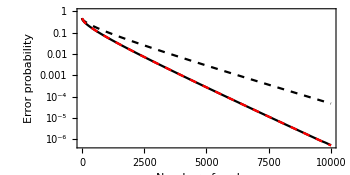

```mathematica
Show[PicRead1,PicRead2]
```

```mathematica
pERRscanner[6000]
SqueezedReading[6000][[1]]
pERRscanner[8000]
SqueezedReading[8000][[1]]
pERRscanner[10000]
SqueezedReading[10000][[1]]
```

0.0000755341

0.0000755339

6.05781×10^-6

6.0578×10^-6

5.17593×10^-7

4.99229×10^-7

```mathematica
(* below we check that the squeezing is <1, i.e., >0 in decibels - It goes to 4dB *)
```

```mathematica
(ReadingSqueezing={#,-10 Log10[SqueezedReading[#][[2,1,2]]]}&/@Range[1,10001,step];)//AbsoluteTiming//Quiet
```

{20.557,Null}

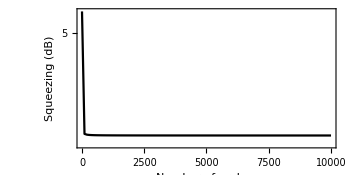

```mathematica
PicReadSqueezing=ListLogPlot[{ReadingSqueezing[[All]]},PlotStyle->{Black},ImageSize->350,Frame->True,FrameLabel-> {Style["Number of probes",FontSize->12,FontFamily->"Helvetica"],Style["Squeezing (dB)",FontSize->12,FontFamily->"Helvetica"]},PlotRange->All,AspectRatio->1/2,Joined->True]
```

```mathematica
(*** ROC ***)
```

```mathematica
FullSimplify[Solve[pFA[η0,nS,nB,m,r,t]==pf,t]]
```

{{t→(m √((2+4 nS-1/r-r) η0))/(√2)+√(m (1+2 nB+(-1+r) η0)) InverseErf[1-2 pf]}}

```mathematica
ROC[η0_,η1_,nS_,nB_,m_,r_,pf_]:=pMD[η1,nS,nB,m,r,(m √((2+4 nS-1/r-r) η0))/(√2)+√(m (1+2 nB+(-1+r) η0)) InverseErf[1-2 pf]]
```

```mathematica
mnum2=500;
```

```mathematica
ROCscan[m_,r_,pf_]:=ROC[η0num2,η1num2,nSnum2,nBnum2,m,r,pf]
```

```mathematica
ROCscan[mnum2,1,0.4]
```

0.0676163

```mathematica
ROCscanOPT[m_,pf_]:=FindMinimum[ROCscan[m,r,pf],{r,rmin[nSnum2]+ϵ,1}][[1]]
```

```mathematica
ROCscanOPT[mnum2,0.4]
```

0.0242668

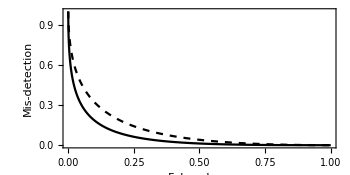

```mathematica
Plot[{ROCscanOPT[mnum2,pf],ROCscan[mnum2,1,pf]},{pf,0,1},PlotStyle->{Black,{Black,Dashed}},Frame->True,PlotRange->All,FrameLabel-> {Style["False alarm",FontSize->12,FontFamily->"Helvetica"],Style["Mis-detection",FontSize->12,FontFamily->"Helvetica"]},ImageSize->350,AspectRatio->1/2]
```